```mathematica
x = 10^-3*{0,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,7.5,8.0,8.5,9.0,9.5,10.0,10.5,11.0,11.5,12.0,12.5,13.0}; (*m*)
P = 10^-3*{1.34,1.34,1.34,1.32,1.29,1.24,1.18,1.12,1.04,0.95,0.85,0.74,0.63,0.52,0.42,0.33,0.26,0.195,0.145,0.11,0.08,0.055,0.038,0.026,0.017,0.011};(*W*)
data={};
For[i=1, i<Length[x]+1, i++, 
AppendTo[data, {x[[i]], P[[i]]}];
]
Print[data]
```

{{0,0.00134},{0.001,0.00134},{0.0015,0.00134},{0.002,0.00132},{0.0025,0.00129},{0.003,0.00124},{0.0035,0.00118},{0.004,0.00112},{0.0045,0.00104},{0.005,0.00095},{0.0055,0.00085},{0.006,0.00074},{0.0065,0.00063},{0.007,0.00052},{0.0075,0.00042},{0.008,0.00033},{0.0085,0.00026},{0.009,0.000195},{0.0095,0.000145},{0.01,0.00011},{0.0105,0.00008},{0.011,0.000055},{0.0115,0.000038},{0.012,0.000026},{0.0125,0.000017},{0.013,0.000011}}

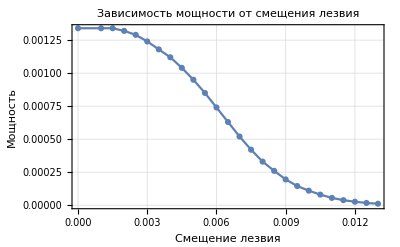

```mathematica
ListLinePlot[data, Frame->True, FrameLabel->{"Смещение лезвия", "Мощность"}, PlotLabel->"Зависимость мощности от смещения лезвия", PlotMarkers->Automatic, GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed]]
```

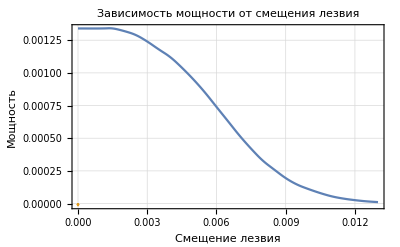

```mathematica
ListLinePlot[{data, DifferentiatorFilter[data, 10000]}, Frame->True, FrameLabel->{"Смещение лезвия", "Мощность"}, PlotLabel->"Зависимость мощности от смещения лезвия", GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed], InterpolationOrder->2]
```

{{0,0.00134},{0.001,0.00134},{0.0015,0.00134},{0.002,0.00132},{0.0025,0.00129},{0.003,0.00124},{0.0035,0.00118},{0.004,0.00112},{0.0045,0.00104},{0.005,0.00095},{0.0055,0.00085},{0.006,0.00074},{0.0065,0.00063},{0.007,0.00052},{0.0075,0.00042},{0.008,0.00033},{0.0085,0.00026},{0.009,0.000195},{0.0095,0.000145},{0.01,0.00011},{0.0105,0.00008},{0.011,0.000055},{0.0115,0.000038},{0.012,0.000026},{0.0125,0.000017},{0.013,0.000011}}

Set::write: Tag Plus in (0.00133911+0.0284324 t-25.359 t^2+5639.27 t^3-1.84786×10^6 t^4+1.86227×10^8 t^5+2.56626×10^9 t^6-1.1284×10^12 t^7+3.95361×10^13 t^8)[t_] is Protected.

0.0284324-50.718 t+16917.8 t^2-7.39143×10^6 t^3+9.31136×10^8 t^4+1.53976×10^10 t^5-7.89882×10^12 t^6+3.16289×10^14 t^7

(0.00133911+0.0284324 t-25.359 t^2+5639.27 t^3-1.84786×10^6 t^4+1.86227×10^8 t^5+2.56626×10^9 t^6-1.1284×10^12 t^7+3.95361×10^13 t^8)[0.00067]

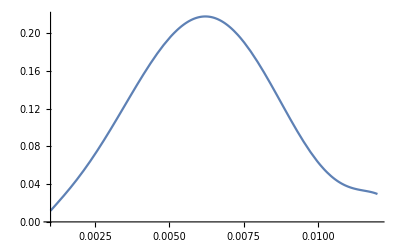

```mathematica
data
func = Fit[data, {1, t, t^2, t^3, t^4,t^5,t^6,t^7,t^8}, t];
data1 = Table[{t,line}, {t, 0, 0.013, 0.001}];
P1=D[func, t]
x0 = func[P[[1]]/2]
Plot[-P1, {t, 0.001, 0.012}]
```

```mathematica
nlm = NonlinearModelFit[data, ]
```